## Classical Mechanics

## Pendulum Waves

In this notebook, we will try and replicate this mesmerizing video demonstration of 15 uncoupled pendula: https://www.youtube.com/watch?v=yVkdfJ9PkRQ.
Let’s start by modeling a single pendulum:

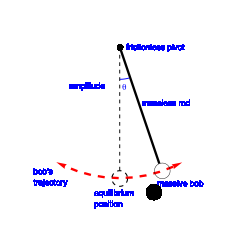

The equation of motion for a pendulum is given by (we’ll derive this later):

### Small-angle Approximation

To solve this analytically, you probably made the “small amplitude” approximation in 8.01. For small amplitudes of θ, we may replace sin(θ(t))→θ(t).

```mathematica
DSolveValue[θ''[t] + g/L θ[t]==0,θ[t],t]
```

C[1] Cos[(√g t)/(√L)]+C[2] Sin[(√g t)/(√L)]

This is a 2^nd order ODE. We therefore need 2 initial conditions to specify the two constants above:

We’ll set the initial displacement at a symbolic value  .

and the initial velocity to zero

```mathematica
smallDisplacementSymbolicSolution[θ0_,g_,L_][t_]=DSolveValue[{θ''[t] + g/L θ[t]==0,θ[0]==θ0,θ'[0]==0},θ[t],t]
```

θ0 Cos[(√g t)/(√L)]

Coding comment: We used the pattern function[paramA_,paramB_][argument_] = ...

Will use this pattern frequently, as it achieves two convenient tasks:
	1.  	Separates arguments and parameters, so we can use forms like: 
			function[paramA,paramB]/@listOfArguments
	2.	Provides a convenient way of assigning symbols to expressions, as opposed to something like:
			expressionRHS /.{paramA->.., paramB->..}

The solution is a simple sinusoidal term with a natural frequency ω=√(g/L). 
Let’s animate one such pendulum, for g=1,L=1,θ_0=π/12

```mathematica
visualizePendulum[length_,color_:White][angle_]:=Graphics[{
{color,Line[{{0,0},length {Sin[angle],-Cos[angle]}}]},
{color,PointSize[Large],Point[length {Sin[angle],-Cos[angle]}]}
},PlotRange->1.025{{-1,1},{-1,0}}]
```

```mathematica
(*#|label:widget_single_pendulum*)
With[{g=1,θ0=π/12,L=1},
Animate[visualizePendulum[L][smallDisplacementSymbolicSolution[θ0,g,L][t]],{t,0,60},AnimationRate->5,AnimationRunning->False,Paneled->False]
]
```

It is now straight-forward to add multiple pendula with different lengths!

```mathematica
(*#|label:widget_multiple_pendula*)
With[{g=1,θ0=π/12},
Animate[Show[
Table[visualizePendulum[length][smallDisplacementSymbolicSolution[θ0,g,length][t]],{length,Subdivide[1/2,1,10]}]
],{t,0,60},AnimationRate->5,AnimationRunning->False,Paneled->False]
]
```